```mathematica
Clear["Global`*"]
```

This Mathematica code is part of the lecture script Introduction to Computational Quantum Mechanics by Roman Schmied. It is licensed under a Creative Commons Attribution-ShareAlike 4.0 International License.

-Graphics-

You can download the associated lecture script at http://arxiv.org/abs/1403.7050

# quantum-mechanical spin and angular momentum operators

```mathematica
SpinQ[S_]:=IntegerQ[2S]&&S≥0
splus[0]={{0}}//SparseArray;
splus[S_?SpinQ]:=splus[S]= SparseArray[Band[{1,2}]->Table[Sqrt[S(S+1)-M(M+1)],{M,S-1,-S,-1}],{2S+1,2S+1}]
sminus[S_?SpinQ]:=Transpose[splus[S]]
sx[S_?SpinQ]:=sx[S]=(splus[S]+sminus[S])/2
sy[S_?SpinQ]:=sy[S]=(splus[S]-sminus[S])/(2I)
sz[S_?SpinQ]:=sz[S]=SparseArray[Band[{1,1}]->Range[S,-S,-1],{2S+1,2S+1}]
id[S_?SpinQ]:=id[S]=IdentityMatrix[2S+1,SparseArray]
```

### operators acting on many spins

an operator a acting on spin k out of a set of n spins-S:

```mathematica
op[S_?SpinQ,n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2S+1,2S+1}:=KroneckerProduct[IdentityMatrix[(2S+1)^(k-1),SparseArray],a,IdentityMatrix[(2S+1)^(n-k),SparseArray]]
```

spin operators acting on spin k out of a set of n spins-S:

```mathematica
Sx[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sx[S]]
Sy[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sy[S]]
Sz[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sz[S]]
Sp[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,splus[S]]
Sm[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=op[S,n,k,sminus[S]]
Id[S_?SpinQ,n_Integer]:=IdentityMatrix[(2S+1)^n,SparseArray]
```

Operadores atuando sobre mais de um spin

```mathematica
SS[S_?SpinQ,n_Integer,k_Integer]/;1≤k≤(n-1):=Sx[S,n,k].Sx[S,n,k+1]+Sy[S,n,k].Sy[S,n,k+1]+Sz[S,n,k].Sz[S,n,k+1] (* Produto escalar de dois spins vizinhos *)
ST2[S_?SpinQ,n_Integer]:=(Sum[Sx[S,n,k],{k,1,n}]).(Sum[Sx[S,n,k],{k,1,n}])+(Sum[Sy[S,n,k],{k,1,n}]).(Sum[Sy[S,n,k],{k,1,n}])+(Sum[Sz[S,n,k],{k,1,n}]).(Sum[Sz[S,n,k],{k,1,n}]) (* Quadrado do spin total *)
STz[S_?SpinQ,n_Integer]:=Sum[Sz[S,n,k],{k,1,n}] (* Componente z do spin total *)
```

Tensores esfericamente irredutíveis

```mathematica
Subscript[Y, 0,0][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=1/Sqrt[4*Pi]*Id[S,n]
Subscript[Y, 1,0][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[3/(4*Pi)]*Sz[S,n,k]
Subscript[Y, 1,1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=-Sqrt[3/(8*Pi)]*Sp[S,n,k]
Subscript[Y, 1,-1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[3/(8*Pi)]*Sm[S,n,k]
Subscript[Y, 2,0][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=-Sqrt[5/(16*Pi)]*(S*(S+1)*Id[S,n]-3*Sz[S,n,k].Sz[S,n,k])
Subscript[Y, 2,1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=-Sqrt[15/(32*Pi)]*(Sz[S,n,k].Sp[S,n,k]+Sp[S,n,k].Sz[S,n,k])
Subscript[Y, 2,-1][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[15/(32*Pi)]*(Sz[S,n,k].Sm[S,n,k]+Sm[S,n,k].Sz[S,n,k])
Subscript[Y, 2,2][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[15/(32*Pi)]*Sp[S,n,k].Sp[S,n,k]
Subscript[Y, 2,-2][S_?SpinQ,n_Integer,k_Integer]/;1≤k≤n:=Sqrt[15/(32*Pi)]*Sm[S,n,k].Sm[S,n,k]
```

Operadores O definidos na equação (4.11) da tese do Victor Quito; note o uso da letra OJ para representar o operador no Mathematica, uma vez que O é uma variável reservada.

```mathematica
NonNegativeQ[J_]:=IntegerQ[J]&&J≥0
OJ[J_?NonNegativeQ,S_?SpinQ,n_Integer,k_Integer]/;1≤ k≤(n-1):=Sum[(-1)^M*Subscript[Y, J,-M][S,n,k].Subscript[Y, J,M][S,n,k+1],{M,-J,J}]
```

### Operadores para um sítio S misto

```mathematica
Operador[sitios_,sitiooperador_,operador_]:={Module[{esquerda,direita,nop},
esquerda=If[sitiooperador>1,Product[2 sitios[[i]]+ 1,{i,1,sitiooperador-1}],0];
direita=If[sitiooperador<Dimensions[sitios][[1]],Product[2 sitios[[i]]+ 1,{i,sitiooperador+1,Dimensions[sitios][[1]]}],0];
If[esquerda>0,nop=KroneckerProduct[IdentityMatrix[esquerda,SparseArray],operador],nop=operador];
If[direita>0,nop=KroneckerProduct[nop,IdentityMatrix[direita,SparseArray]]];
nop]}
```

```mathematica
OJg[J_?NonNegativeQ,sitios_,sitiooperador_]:=Sum[(-1)^M*(Operador[sitios,sitiooperador,Subscript[Y, J,-M][sitios[[sitiooperador]],1,1]][[1]]).(Operador[sitios,sitiooperador+1,Subscript[Y, J,M][sitios[[sitiooperador+1]],1,1]][[1]]),{M,-J,J}]  (*Operador OJ *)
OJ2v[J_?NonNegativeQ,sitios_,sitiooperador_]:=Sum[(-1)^M*(Operador[sitios,sitiooperador,Subscript[Y, J,-M][sitios[[sitiooperador]],1,1]][[1]]).(Operador[sitios,sitiooperador+2,Subscript[Y, J,M][sitios[[sitiooperador+2]],1,1]][[1]]),{M,-J,J}] (*Operador OJ para segundos vizinhos *)
```

```mathematica
STzg[sitios_]:=Sum[Operador[sitios,k,Sz[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]  (*Sz do spin total*)
STpg[sitios_]:=Sum[Operador[sitios,k,Sp[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]  (*Sp do spin total*)
STmg[sitios_]:=Sum[Operador[sitios,k,Sm[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]  (*Sp do spin total*)
```

```mathematica
ST2g[sitios_]:=(Sum[Operador[sitios,k,Sx[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]).(Sum[Operador[sitios,k,Sx[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}])+(Sum[Operador[sitios,k,Sy[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]).(Sum[Operador[sitios,k,Sy[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}])+(Sum[Operador[sitios,k,Sz[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]).(Sum[Operador[sitios,k,Sz[sitios[[k]],1,1]][[1]],{k,1,Dimensions[sitios][[1]]}]) (* Quadrado do spin total*)
```

```mathematica
Yg[sitios_,sitiooperador_,J_,M_]:=Operador[sitios,sitiooperador,Subscript[Y, J,-M][sitios[[sitiooperador]],1,1]][[1]] (* Operadores Y fornecendo o sítio*)
```

# Funções de renormalização

## Funções úteis

```mathematica
KtoJ[k1_,k2_]:=(1/(16π))(12k1+15k2)//Simplify
KtoD[k2_]:=(15/(8π))k2//Simplify
KtoJD[k1_,k2_]:={KtoJ[k1,k2],KtoD[k2]}//Simplify
KtoJ::usage="KtoJ[K_1, K_2] converte os valores de {K_1, K_2} -> {J}";
KtoD::usage="KtoD[K_2] converte os valores de {K_2} -> {D}";
KtoJD::usage="KtoJD[K_1, K_2] converte os valores de {K_1, K_2} -> {J, D}";
```

```mathematica
JtoK1[j_,d_]:=4π j/3 - 2π d/3 //Simplify
DtoK2[d_]:=8π d/15//Simplify
JDtoK[j_,d_]:={JtoK1[j,d],DtoK2[d]}//Simplify
JtoK1::usage="JtoK1[J, D] converte os valores de {J, D} -> {K_1}";
DtoK2::usage="DtoK[D] converte os valores de {D} -> {K_2}";
JDtoK::usage="JDtoK[J, D] converte os valores de {J, D} -> {K_1, K_2}";
```

```mathematica
AngJD[j_,d_]:=Module[{θ},If[d≠0&&Abs[j/d]<10^-10,θ=If[d>0,90,-90],θ=If[j≠0,If[j>0,(180 ArcTan[d/j])/π,(180 ArcTan[d/j])/π+180],If[d>0,90,If[d<0,-90,0]]];If[θ>180,θ=θ-360];θ]]
AngJD::usage="AngJD[J, D] retorna o angulo entre os valores J e D em graus";
```

```mathematica
AngK[k1_,k2_]:=Module[{θ,j,d},{j,d}=N[KtoJD[k1,k2]];AngJD[j,d]]
AngK::usage="AngK[K_1, K_2] retorna o angulo entre os coeficientes K em graus";
```

```mathematica
Num63[n_]:=(Total[MatrixPower[{{4, 2}, {2, 1}},n].{0, 1}])
Num63::usage="Num63[n] retorna o número n de elementos para uma cadeia 63";
```

```mathematica
ReescalarCadeia[array_]:=(Module[{a=Max[Abs[array[[All,1;;2]]]],cadeiaReescalada},
cadeiaReescalada=Transpose[{1/a,1/a,1,1,1} Transpose[array]];
{a,cadeiaReescalada}])
ReescalarCadeia::usage="ReescalarCadeia[cadeia] retorna {fator, cadeiareescalada} com fator sendo o valor utilizado para tornar o maior acoplamento como 1";
```

```mathematica
RetornarCadeia[array_,fator_]:=(Module[{cadeiaReescalada},
cadeiaReescalada=Transpose[{fator,fator,1,1,1} Transpose[array]];
cadeiaReescalada])
```

```mathematica
RazJD[j_,d_]:=(If[j!=0,d/j,0])
```

```mathematica
FiltrarBordar[dados_]:=(Module[{M={},Tdado=dadosᵀ,i=1},
While[i<=Length[Tdado],
If[Not[Tdado[[i,3]]],M=Insert[M,Tdado[[i,All]],-1]];
i++
];
Mᵀ
])
```

## Função que criam um H

### Hamiltoniano

```mathematica
H[sitios_,k_]:=Module[{J,n},Sum[Sum[k[[J]]*OJg[J,sitios,n],{J,1,2}],{n,1,Dimensions[sitios][[1]]-1}]]
H::usage="H[{S_1,S_2,...S_N},{K_1,K_2}] retorna um hamiltoniano para N sítions com spins distintos com o mesmo par de acoplamentos {K_1,K_2}";
```

### Criar Hamiltoniano com base cadeia

É preciso fornecer os valores individuais dos spins e dos k_a e k_b para cada ligação, um exemplo cadeia={{K_a_1,K_a_2,S_1,1,1},{K_b_1,K_b_2,S_2,2,2},{K_a_1,K_a_2,S_3,3,3},{0,0,S_4,4,4}}

```mathematica
Hcadeia[array_]:=(
	Module[{cadeiahcad,k,s,h,H,kn,i},
	k=array[[All,1;;2]];
	s=array[[All,3]];
For[i=1,i<Length[s],i++,h[i]=Sum[k[[i,J]]*OJg[J,s,i],{J,1,2}]];
H=Sum[h[n],{n,1,Dimensions[s][[1]]-1}];
H])
Hcadeia::usage="H[{{K_a_1,K_a_2,S_1,1},{K_b_1,K_b_2,S_2,2},{K_a_1,K_a_2,S_3,3}, ..., {0,0,S_n,4}}] retorna um hamiltoniano para uma cadeia com N sítions e acoplamentos distintos";
```

## Funções de calculo dos coeficientes de primeira ou segunda ordem

### Coeficientes G

```mathematica
Gj[sitio_,vecs_,J_,M_,min_,dim_,k_]:=(Module[{e0},
e0=vecs[[min]].H[sitio,k].vecs[[min]];

2Sum[If[i==min,0,(vecs[[min]].Yg[sitio,1,J,-M].vecs[[i]])(vecs[[i]].Yg[sitio,Dimensions[sitio][[1]],J,M].vecs[[min]])/(e0-vecs[[i]].H[sitio,k].vecs[[i]])],{i,1,dim}]//Simplify])
Gj::usage="Gj[sítios, vetores, J, M, posição do vetor com menor auto valor, dimensão, {K_1, K_2}";
```

### Coeficientes F

```mathematica
Fj[sitio_,vetor_,sitiooperando_,J_,S_]:=(Module[{vec},
vec={1};
Do[vec=Insert[vec,0,-1],Round[2S]];
If[(S==1/2&&J==2),0,N[Round[vetor.Yg[sitio,sitiooperando,J,0].vetor/vec.Subscript[Y, J,0][S,1,1].vec,10^-12]]]])
```

## Função para encontrar o gap

```mathematica
CalcularGap[Mgap_,precisao_:-8]:=(
Module[{norm=Max[Abs[Mgap]],H,en,m=20},
H=N[Mgap]/norm;
If[Length[H]>81,
en=-Eigenvalues[-H,m,Method->{Arnoldi,MaxIterations->10^5,Criteria->RealPart}];
en=DeleteDuplicates[N[Sort[Round[Sort[en], 10^precisao]]]];
While[Length[en]==1&&m<=Length[H],
en=-Eigenvalues[-H,m,Method->{Arnoldi,MaxIterations->10^5,Criteria->RealPart}];
en=DeleteDuplicates[N[Sort[Round[Sort[en], 10^precisao]]]];
m=m+5],
en=DeleteDuplicates[N[Sort[Round[Sort[Eigenvalues[H]], 10^precisao]]]];
];
If[Length[en]1>1,norm*(en[[2]]-en[[1]]),0]])
CalcularGap::usage="CalcularGap[Matriz, precisao], retorna a diferença entre o primeiro e segundo auto valor distintos de uma matriz hermitiana, precisao padrão é -8 (equivalente é 10^-8)";
```

```mathematica
GapCadeia[array_,precisao_:-8]:=CalcularGap[Hcadeia[array],precisao]
GapCadeia::usage="GapCadeia[cadeia], retorna a diferença entre o primeiro e segundo auto valor de um hamiltoniano gerado a partir de uma cadeia do tipo {{K_a_1,K_a_2,S_1,1,1},{K_b_1,K_b_2,S_2,2,2},{K_a_1,K_a_2,S_3,3,3}, ..., {0,0,S_N,N,N}}";
```

## Criação cadeia aperiódicas

```mathematica
CadeiaFibonacci[m_,kb1_,kb2_,razao_:10]:=(
Module[{ka1,ka2,j,l,st},
{ka1,ka2}={kb1,kb2}/razao;
l=j=2;
{st[1],st[2]}={{ka1,ka2,1, 1,1},{kb1,kb2,1, 2,2}};
If[kb1≠0,
While[l≤m,{If[st[j][[1]]==ka1,{st[l+1]={ka1,ka2,1,l+1,l+1},st[l+2]={kb1,kb2,1,l+2,l+2},l=l+2,j=j+1}];
If[st[j][[1]]==kb1,{st[l+1]={ka1,ka2,1, l+1, l+1},l=l+1,j=j+1}]};];
st[m+1]={0.,0.,1, m+1,m+1},

While[l≤m,{If[st[j][[2]]==ka2,{st[l+1]={ka1,ka2,1,l+1,l+1},st[l+2]={kb1,kb2,1,l+2,l+2},l=l+2,j=j+1}];
If[st[j][[2]]==kb2,{st[l+1]={ka1,ka2,1, l+1, l+1},l=l+1,j=j+1}]};];
st[m+1]={0.,0.,1, m+1,m+1}];
Array[st,m+1]]
)
CadeiaFibonacci::usage="CadeiaFibonacci[L, K_b1, K_b2, Razao: 10] cria uma cadeia utilizando a inflação (a→ab, b→a) com S = 1 {{K_a_1,K_a_2,S, 1, 1},{K_b_1,K_b_2, S,2,2},{K_a_1,K_a_2, S,3,3}, ..., {0,0, S, L+1, L+1}}, a razão padrão é 10";
```

```mathematica
CadeiaFibonacciSpinMeio[m_,kb1_,razao_:10]:=(
Module[{ka1,j,l,cadeia,st},
ka1=kb1/razao;
l=j=2;
cadeia=Array[st,m+1];
st[1]={ka1,0,1/2, 1,1};
st[2]={kb1,0,1/2, 2,2};

While[l≤m,{If[st[j][[1]]==ka1,{st[l+1]={ka1,0,1/2,l+1,l+1},st[l+2]={kb1,0,1/2,l+2,l+2},l=l+2,j=j+1}];
If[st[j][[1]]==kb1,{st[l+1]={ka1,0,1/2, l+1, l+1},l=l+1,j=j+1}]};];
st[m+1]={0.,0.,1/2, m+1,m+1};

cadeia]
)
CadeiaFibonacciSpinMeio::usage="CadeiaFibonacci[L, K_b, Razao: 10] cria uma cadeia utilizando a inflação (a→ab, b→a) com S = 1/2 {{K_a,0,S, 1, 1},{K_b,0, S,2,2},{K_a,0, S,3,3}, ..., {0,0, S, L+1, L+1}}, a razão padrão é 10";
```

```mathematica
Cadeia63[m_,kb1_,kb2_,razao_:10]:=(
Module[{ka1,ka2,j,l,cadeia,st},
ka1=kb1/razao;
ka2=kb2/razao;
j=2;
l=3;
cadeia=Array[st,m+1];(* Criando um vetor que guarda os tipos de ligação*)
st[1]={kb1,kb2,1, 1,1};
st[2]={ka1,ka2,1, 2,2};
st[3]={ka1,ka2,1, 2,3};
If[kb1≠0,
While[l≤m,{If[st[j][[1]]==ka1,{
st[l+1]={kb1,kb2,1,l+1,l+1},
st[l+2]={ka1,ka2,1,l+2,l+2},
st[l+3]={kb1,kb2,1,l+3,l+3},
st[l+4]={ka1,ka2,1,l+4,l+4},
st[l+5]={ka1,ka2,1,l+5,l+5},
st[l+6]={ka1,ka2,1,l+6,l+6},
l=l+6,
j=j+1
}];
If[st[j][[1]]==kb1,{
st[l+1]={kb1,kb2,1, l+1, l+1},
st[l+2]={ka1,ka2,1, l+2, l+2},
st[l+3]={ka1,ka2,1, l+3, l+3},
l=l+3,
j=j+1
}]};](*a->babaaa b->baa*);
st[m+1]={0.,0.,1, m+1,m+1},
While[l≤m,{If[st[j][[2]]==ka2,{
st[l+1]={kb1,kb2,1,l+1,l+1},
st[l+2]={ka1,ka2,1,l+2,l+2},
st[l+3]={kb1,kb2,1,l+3,l+3},
st[l+4]={ka1,ka2,1,l+4,l+4},
st[l+5]={ka1,ka2,1,l+5,l+5},
st[l+6]={ka1,ka2,1,l+6,l+6},
l=l+6,
j=j+1
}];
If[st[j][[2]]==kb1,{
st[l+1]={kb1,kb2,1, l+1, l+1},
st[l+2]={ka1,ka2,1, l+2, l+2},
st[l+3]={ka1,ka2,1, l+3, l+3},
l=l+3,
j=j+1
}]};](*a->babaaa b->baa*);
st[m+1]={0.,0.,1, m+1,m+1}
];
cadeia]
)
Cadeia63::usage="Cadeia63[L, K_b1, K_b2, Razao: 10] cria uma cadeia utilizando a inflação (a→babaaa, b→baa) com S = 1 {{K_a_1,K_a_2,S, 1, 1},{K_b_1,K_b_2, S,2,2},{K_a_1,K_a_2, S,3,3}, ..., {0,0, S, L+1, L+1}}, a razão padrão é 10";
```

## Identificar blocos únicos

```mathematica
BlocosUnicos[array_]:=(
Module[{j=1,blocos={},contagem={},Kn,blocon,linha},
While[j<Dimensions[array][[1]],
	Kn={array[[j,1]],array[[j,2]]};
	blocon={array[[j,3]]};
	While[Kn=={array[[j,1]],array[[j,2]]}&&j<Length[array],
	blocon=Insert[blocon,array[[j+1,3]],-1];
j=j+1;
];
linha={Kn,blocon};
If[Not[MemberQ[blocos,linha]],{blocos=Insert[blocos,linha,-1],contagem=Insert[contagem,1,-1]},
contagem[[Flatten[Position[blocos,linha][[1]]]]]=contagem[[Flatten[Position[blocos,linha][[1]]]]]+1
];
];
{blocos,contagem}]);
BlocosUnicos::usage="BlocosUnicos[Cadeia], retorna os diferentes blocos da cadeia e uma contagem do detes";
```

## Calcular Gap e S efetivo dos blocos únicos

```mathematica
GapsBlocosUnico[array_]:=(
Module[{j=1,Gapspinbu={},razao={},K1=array[[1;;-2,1;;2]],bloco,razgapvizinho,imax,jb,db,ja,da,,k,Hgapunico,maxhpunico,energiabu,minvecgu,Sgu,gabc,θi,max,contagem},
{bloco,contagem}=BlocosUnicos[array];
While[j<=Length[bloco],
	Hgapunico=H[bloco[[j,2]],{bloco[[j,1,1]],bloco[[j,1,2]]}];
	gabc=CalcularGap[Hgapunico];
	Gapspinbu=Insert[Gapspinbu,{gabc},-1];
	j++];
imax=Position[Gapspinbu,Max[Gapspinbu[[All,1]]]][[1,1]];
{jb,db}=KtoJD[bloco[[imax,1,1]],bloco[[imax,1,2]]];
max=Position[Gapspinbu,Max[Gapspinbu]][[1,1]];
razgapvizinho=GapVizinho[array,bloco[[max,1]],bloco[[max,2]],Gapspinbu[[max]][[1]]];
{Gapspinbu,bloco,razgapvizinho,contagem[[max]]}
])
GapsBlocosUnico::usage="GapsBlocosUnico[Cadeia], retorna {Gaps, Blocos, Razão do mairo gap com seus vizinhos, Número de sítios com maior gap}";
```

```mathematica
GapVizinho[array_,k_,spins_,gap_]:=(
Module[{inicio,final,j,GBU,K,blocobu,linhabu,θi},
GBU={};
j=1;
While[j<Dimensions[array][[1]]&&Dimensions[GBU][[1]]<10,
K={array[[j]][[1]],array[[j]][[2]]};
If[K==k,
	inicio=j;
	blocobu={array[[j,3]]};
	While[K=={array[[j,1]],array[[j,2]]}&&j<Dimensions[array][[1]],
	blocobu=Insert[blocobu,array[[j+1]][[3]],-1];
	j++;];
final=j;
linhabu={inicio,final,BlocoVizionhoEsquerdo[array,inicio]/gap,BlocoVizionhoDireita[array,final]/gap,AngVizinhoEsquerda[array,inicio],AngVizinhoDireita[array,final]};
If[blocobu==spins&&k==K,GBU=Insert[GBU,linhabu,-1]];
];
j=j+1;
];
GBU])
```

```mathematica
BlocoVizionhoDireita[cad_,j_]:=Module[{k,i,l,Ja,Da,S},k=cad⟦j,1;;2⟧;If[k!={0,0},i=j;l=j;S={cad⟦j,3⟧};While[cad⟦i⟧⟦1;;2⟧==k&&i<Dimensions[cad][[1]],{S=Insert[S,cad⟦l+1,3⟧,-1],l++,i++}];
CalcularGap[H[S,k]],0]]
```

```mathematica
BlocoVizionhoEsquerdo[cad_,j_]:=Module[{k,i,l,S},If[j>1,k=cad⟦j-1,1;;2⟧;i=j-1;l=j;S={cad⟦j,3⟧};While[i≥1&&cad⟦i,1;;2⟧==k,{S=Insert[S,cad⟦i,3⟧,1],i--}];If[Dimensions[S]⟦1⟧>1,CalcularGap[H[S,k]],0],0]]
```

```mathematica
AngVizinhoDireita[cad_,j_]:=Module[{k,i,l,Ja,Da,S},k=cad⟦j,1;;2⟧;If[k!={0,0},i=j;l=j;S={cad⟦j,3⟧};While[cad⟦i⟧⟦1;;2⟧==k&&i<Dimensions[cad][[1]],{S=Insert[S,cad⟦l+1,3⟧,-1],l++,i++}];
{Ja,Da}={KtoJ[k[[1]],k[[2]]],KtoD[k[[2]]]};
AngJD[Ja,Da],0]]
```

```mathematica
AngVizinhoEsquerda[cad_,j_]:=Module[{k,i,l,Ja,Da,S},If[j>1,k=cad⟦j-1,1;;2⟧;i=j-1;l=j-1;S={cad⟦j,3⟧};While[i≥1&&cad⟦i,1;;2⟧==k,{S=Insert[S,cad⟦i,3⟧,1],i--}];{Ja,Da}=KtoJD[k[[1]],k[[2]]];If[Dimensions[S]⟦1⟧>1,AngJD[Ja,Da],0],0]]
```

## Calculando as novas ligações

```mathematica
NovaLigação[cad_]:=(
Module[{Lig=GapsBlocosUnico[cad],gapvizinho,Gnl,Anl,pnl,Stil,vals,vecs,minvecnl,stznl,GNL,k,minnl,vecsanl,dimnl,bloconl,min,ListaS,contagem},
{Gnl,Anl,gapvizinho,contagem}=Lig;
pnl=Position[Gnl,Max[Gnl[[All,1]]]][[1,1]];
{vals,vecs,minvecnl,min}=Vetormin[Anl[[pnl,2]],Anl[[pnl,1]]];
ListaS=calcS[vecs,Anl[[pnl,2]],min];
Stil=minvecnl.ST2g[Anl[[pnl,2]]].minvecnl;
Stil=Round[-0.5+0.5 Sqrt[1+4Stil],1/2];
If[Stil>0,
	stznl=Round[minvecnl.STzg[Anl[[pnl,2]]].minvecnl,1/2];
	GNL={Anl[[pnl]][[1]],Anl[[pnl]][[2]],{Fj[Anl[[pnl,2]],minvecnl,1,1,Stil],Fj[Anl[[pnl,2]],minvecnl,1,2,Stil],Fj[Anl[[pnl,2]],minvecnl,Length[Anl[[pnl]][[2]]],1,Stil],Fj[Anl[[pnl,2]],minvecnl,Length[Anl[[pnl]][[2]]],2,Stil]},{Stil,stznl}}
];
If[Stil==0,
	k[1]=Anl[[pnl]][[1]][[1]];
	k[2]=Anl[[pnl]][[1]][[2]];
	minnl=minnl=Flatten[Position[vals,Min[vals]]][[1]];
	dimnl=Dimensions[vecs][[1]];
	bloconl=Anl[[pnl,2]];
	GNL={Anl[[pnl]][[1]],Anl[[pnl]][[2]],{Gj[bloconl,vecs,1,0,minnl,dimnl,{k[1],k[2]}],Gj[bloconl,vecs,2,0,minnl,dimnl,{k[1],k[2]}]},{Stil}};
];
{GNL,Lig,ListaS,gapvizinho,contagem}])
```

```mathematica
calcS[vec_,spin_,min_]:=(Module[{j,S},
S={};

For[j=1,j<=Length[min],j++,S=Insert[S,Round[vec[[min[[j]]]].ST2g[spin].vec[[min[[j]]]]],-1]];
S])
```

## Auto vetores e o auto vetor associado ao menor auto valor com máximo de S_z

Achar o vetor com Sz >0 associado ao menor auto valor é necessário para calcular o valor de F

```mathematica
Vetormin[spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,Stil,i, Hvetormin, rescale},
i=2;
{vals,vecs,vecmin,sz1,min}=metodo[1][spins,k/Max[Abs[k]]];
Stil=vecmin.ST2g[spins].vecmin;
Stil=Round[-0.5+0.5 Sqrt[1+4Stil],1/2];
While[Abs[sz1-Stil]>0.001&&i<=10,{{vals,vecs,vecmin,sz1,min}=metodo[i][spins,k/Max[Abs[k]]],i++;}];
N[{vals*Max[Abs[k]],vecs,vecmin,min},8]])
```

#### Metodo normal

```mathematica
metodo[1][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = H[spins,k];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[2][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = H[spins,k];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo Banded

```mathematica
metodo[3][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = H[spins,k];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[4][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = H[spins,k];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo SetPrecision32

```mathematica
metodo[5][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[H[spins,k],32];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[6][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ H[spins,k],32];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo SetPrecision64

```mathematica
metodo[7][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[H[spins,k],64];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[8][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ H[spins,k],64];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

#### Metodo SetPrecision128

```mathematica
metodo[9][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[H[spins,k],128];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

```mathematica
metodo[10][spins_,k_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ H[spins,k],128];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[spins].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[spins].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1,min}])
```

## Renormalização

### Renormalizar bloco S’>0

```mathematica
ren1[cadeia1_,inicialren_,finalren_, Fs_, Stil_]:=(
Module[{cadeiaren1,inicalren1,finalrean1,iren1,Fren1},
cadeiaren1=cadeia1;
inicalren1=inicialren;
finalrean1=finalren;
iren1=0;
Fren1=Fs;
If[inicialren>1 ,{
cadeiaren1[[inicalren1-1]]={cadeiaren1[[inicalren1-1,1]] Fren1[[1]],cadeiaren1[[inicalren1-1,2]] Fren1[[2]],cadeiaren1[[inicalren1-1,3]],cadeiaren1[[inicalren1-1,4]],cadeiaren1[[inicalren1-1,5]]};
cadeiaren1[[finalrean1]]={cadeiaren1[[finalrean1,1]] Fren1[[3]],cadeiaren1[[finalrean1,2]] Fren1[[4]],Stil,cadeiaren1[[finalrean1,4]],cadeiaren1[[finalrean1,5]]};
While[(inicalren1+iren1)<(finalrean1),cadeiaren1[[(inicalren1+iren1)]]={0};iren1++]}];
If[inicialren==1,{
cadeiaren1[[finalrean1]]={cadeiaren1[[finalrean1,1]] Fren1[[3]],cadeiaren1[[finalrean1,2]] Fren1[[4]],Stil,cadeiaren1[[finalrean1,4]],cadeiaren1[[finalrean1,5]]};
While[(inicalren1+iren1)<finalrean1,cadeiaren1[[(inicalren1+iren1)]]={0};iren1++]}];
DeleteCases[cadeiaren1,{0}]])
```

### Renormalizar bloco S’=0

```mathematica
ren0[cadeia1_,inicialren_,finalren_, Gs_]:=(
Module[{cadeiaren0,inicalren0,finalrean0,iren0,Gren0},
cadeiaren0=cadeia1;
inicalren0=inicialren;
finalrean0=finalren;
iren0=0;
Gren0=Gs;
If[inicalren0>1,{cadeiaren0[[inicalren0-1]]={cadeiaren0[[inicalren0-1,1]]cadeiaren0[[finalrean0,1]] Gren0[[1]],cadeiaren0[[inicalren0-1,2]]cadeiaren0[[finalrean0,2]] Gren0[[2]],cadeiaren0[[inicalren0-1,3]],cadeiaren0[[inicalren0-1,4]],cadeiaren0[[inicalren0-1,5]]};While[(inicalren0+iren0)<=finalrean0,cadeiaren0[[(inicalren0+iren0)]]={0};iren0++]}];
If[inicalren0==1,While[(inicalren0+iren0)<=finalrean0,cadeiaren0[[(inicalren0+iren0)]]={0};iren0++]];
DeleteCases[cadeiaren0,{0}]])
```

### Renormalização aplicada a cadeia

```mathematica
Renormalizar[cadeia_]:=(
Module[{Aren,gapvizinho,cadren,kren,blocoren,kb1ren,kb2ren,Sren,jren,d,spinsren,inicialren,finalren,iren,Lig,ListaS,fator,inf,contagem,isborda},
{fator,cadren}=ReescalarCadeia[cadeia];
{Aren,Lig,ListaS,gapvizinho,contagem}=NovaLigação[cadren];
kren=Aren[[1]];
blocoren=Aren[[2]];
kb1ren=kren[[1]];
kb2ren=kren[[2]];
jren=1;
d=Dimensions[cadren][[1]];
If[Not[Pararrenormalizar[Aren[[4,1]],blocoren,cadren]],jren=d];
While[jren<d,
If[cadren[[1,1;;2]]=={0.,0.},cadren=Delete[cadren,1];jren=1];
	spinsren={};
	If[{cadren[[jren,1]],cadren[[jren,2]]}==kren,{spinsren={cadren[[jren,3]]},inicialren=jren}];
	While[{cadren[[jren,1]],cadren[[jren,2]]}==kren,spinsren=Insert[spinsren,cadren[[jren+1]][[3]],-1];jren++;];
         finalren=jren;
	If[spinsren==blocoren&&Aren[[4,1]]==0, {cadren=ren0[cadren,inicialren,finalren, Aren[[3]]],jren=jren-(finalren-inicialren)-1}];
	If[spinsren==blocoren&&Aren[[4,1]]>0, {cadren=ren1[cadren,inicialren,finalren, Aren[[3]],Aren[[4,1]]],jren=jren-(finalren-inicialren)}];
          d=Dimensions[cadren][[1]];
	If[Not[Pararrenormalizar[Aren[[4,1]],blocoren,cadren]],jren=d,jren++];
];
iren=1;
While[iren≤Dimensions[cadren][[1]],cadren[[iren,5]]=iren;iren++];
inf={Length[cadeia],Max[{gapvizinho[[All,3]],gapvizinho[[All,4]]}],AngK[kb1ren,kb2ren],GetAngRaz[gapvizinho]};
If[contagem==1&&Length[cadeia]>10,isborda=True,isborda=False];
{cadren,ListaS,inf,fator,isborda}])
```

```mathematica
Pararrenormalizar[S_,bloco_,cadren_]:=(Module[{a},a = False;
If[S>0  && Dimensions[bloco][[1]]<Dimensions[cadren][[1]],
	a =True
];
If[S==0 && Dimensions[bloco][[1]]<=Dimensions[cadren][[1]]-2,
a = True
];
a])
```

```mathematica
GetAngRaz[raz_]:=(Module[{max,l},
If[Max[raz[[All,3]]]>=Max[raz[[All,4]]],{max=Position[raz[[All,3]],Max[raz[[All,3]]]][[1,1]],l=5},{max=Position[raz[[All,4]],Max[raz[[All,4]]]][[1,1]],l=6}];
raz[[max,l]]])
```

## S final cadeia

```mathematica
Stotalcad[array_]:=(Module[{vals,vecs,min,vecmin,sz1,Stil,i, Hvetormin, rescale,x},
x=array;
x[[All,1]]=array[[All,1]]/Max[Abs[array[[All,1;;2]]]];
x[[All,2]] = array[[All,2]]/Max[Abs[array[[All,1;;2]]]];
i=2;
{vals,vecs,vecmin,sz1}=metodoStotalcad[1][x];
Stil=vecmin.ST2g[x[[All,3]]].vecmin;
Stil=Round[-0.5+0.5 Sqrt[1+4Stil],1/2];
While[Abs[sz1-Stil]>0.001&&i<=10,{{vals,vecs,vecmin,sz1}=metodoStotalcad[i][x],i++}];
vecmin.ST2g[x[[All,3]]].vecmin])
```

#### Metodo normal

```mathematica
metodoStotalcad[1][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = Hcadeia[array];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[2][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = Hcadeia[array];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo Banded

```mathematica
metodoStotalcad[3][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin =  Hcadeia[array];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[4][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin = Hcadeia[array];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin,Method->"Banded"];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo SetPrecision32

```mathematica
metodoStotalcad[5][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[Hcadeia[array],32];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[6][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ Hcadeia[array],32];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo SetPrecision64

```mathematica
metodoStotalcad[7][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[Hcadeia[array],64];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[8][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ Hcadeia[array],64];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

#### Metodo SetPrecision128

```mathematica
metodoStotalcad[9][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin },
Hvetormin = SetPrecision[Hcadeia[array],128];
Hvetormin=Hvetormin;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals ,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

```mathematica
metodoStotalcad[10][array_]:=(Module[{vals,vecs,min,vecmin,sz1,sz2,i, Hvetormin, rescale},
Hvetormin =SetPrecision[ Hcadeia[array],128];
rescale=Max[Abs[Hvetormin]];
Hvetormin=Hvetormin/rescale;
{vals,vecs}=Eigensystem[Hvetormin];
vals=N[Round[vals * rescale,10^-12]];
min=Flatten[Position[vals,Min[vals]]];
vecmin=vecs[[min[[1]]]];
sz1=vecs[[min[[1]]]].STzg[array[[All,3]]].vecs[[min[[1]]]];

For[i=1,i<Length[min],sz2=vecs[[min[[i]]]].STzg[array[[All,3]]].vecs[[min[[i]]]];
If[sz2>sz1,{sz1=sz2,vecmin=vecs[[min[[i]]]]}],i++];
{vals,vecs,vecmin,sz1}])
```

## Imagem

### Ligações

```mathematica
fraca[1]=-Graphics-;
forte[1]=-Graphics-;
isolado[1]=-Graphics-;
```

### Gerar Imagem

```mathematica
ImagemCadeia[array_]:=(Module[{cadeiaimagem,minimoimagem,maximoimagem,Cadeiaimagem,cadimagem},
cadeiaimagem=Abs[Transpose[{array[[All,1]],array[[All,3]]}]];
minimoimagem=Min[DeleteCases[cadeiaimagem[[All,1]],0.]];
maximoimagem=Max[DeleteCases[cadeiaimagem[[All,1]],0.]];
If[minimoimagem>0,cadeiaimagem[[All,1]]=cadeiaimagem[[All,1]] /.x_/;0<x<maximoimagem->Max[cadeiaimagem[[1;;Dimensions[cadeiaimagem][[1]]-1,1]]]/2;];
Do[{cadeiaimagem [[i,2]]=Rasterize[Style[cadeiaimagem[[i,2]],FontFamily->"Calibri",16]]},{i,1,Length[cadeiaimagem]}];
cadeiaimagem=cadeiaimagem/.maximoimagem/2->fraca[1];
cadeiaimagem=cadeiaimagem/.maximoimagem->forte[1];
cadeiaimagem=cadeiaimagem/. 0.->isolado[1];
cadimagem={};
Do[cadimagem=Insert[cadimagem,Show[cadeiaimagem[[i,1]],cadeiaimagem[[i,2]]],-1],{i,1,Length[cadeiaimagem]}];
ImageResize[ImageAssemble[ConformImages[cadimagem]],{Automatic,40}]])
```

# Cadeia de Fib spin 1

```mathematica
num=Fibonacci[15];
Off[Eigenvalues::arh];
Off[Eigensystem::arh];
Jb=1;
θ=10Degree;
{Kb1,Kb2}=N[JDtoK[Jb Cos[θ],Jb Sin[θ]]];
cadeia[0]=CadeiaFibonacci[num-1,Kb1,Kb2];
i=1;
While[True,
{cadeia[i],spins[i],dados[i],fator[i],isborda[i]}=Renormalizar[cadeia[i-1]];
If[Not[Length[cadeia[i-1]]!=Length[cadeia[i]]],{i=i-1,Break[]}];
i++;
];
```

```mathematica
Fator=Array[fator,i];
gap=GapCadeia[cadeia[i]]*Product[Fator[[i]],{i,1,Length[Fator]}];
{Spins,Dados}=FiltrarBordar[{Array[spins,i],Array[dados,i],Array[isborda,i]}][[1;;2]];
{L,RazaoGaps,θb,θa}=Transpose[Dados];
```

```mathematica
Print["Inicial:  "]; ImagemCadeia[cadeia[0][[1;;15]]]
Print["final:  "]; ImagemCadeia[cadeia[i]]
Print["Gap final: ",N[gap,3]]
```

Inicial:

-Graphics-

final:

-Graphics-

Gap final: 0.0000873325

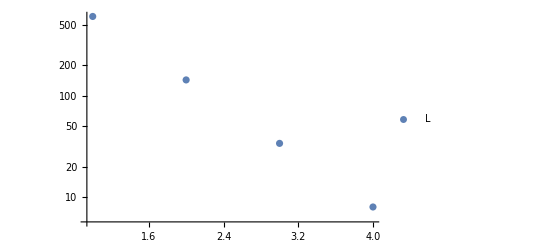

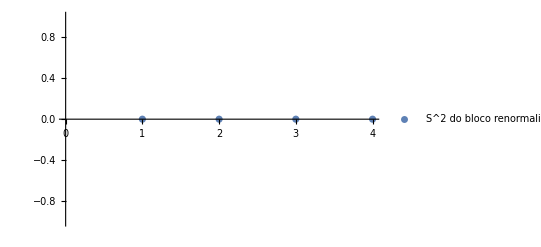

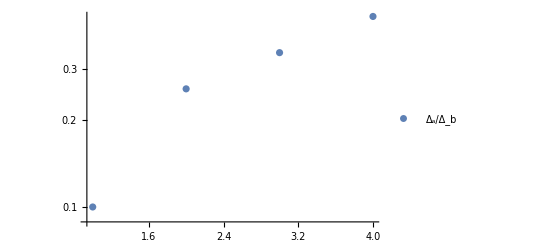

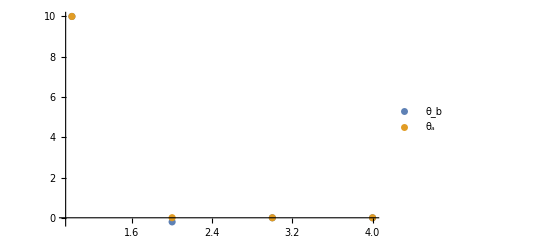

```mathematica
ListLogPlot[L,PlotRange->All,PlotLegends->{"L"}]
ListPlot[Spins[[All,1]],PlotLegends->{"S^2 do bloco renormalizado"}]
ListLogPlot[RazaoGaps,PlotRange->All,PlotLegends->{"Δ_a/Δ_b"}]
ListPlot[{θb,θa},PlotRange->All,PlotLegends->{"θ_b","θ_a"}]
```